```mathematica
ClearAll["Global`*"]


SetOptions[Plot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,Thickness[0.005]}, PlotRange->All];
SetOptions[ListPlot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,PointSize[0.005]}, PlotRange->All];

SetOptions[ListPointPlot3D,LabelStyle->Directive[Black, Bold, FontSize-> 16], PlotStyle-> {Lighter[Blue],PointSize[0.005],Thickness[0.007]}, PlotRange->All];


SetOptions[ListLogPlot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,PointSize[0.005]}, PlotRange->All];
SetOptions[ListLinePlot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,Thickness[0.005]}, PlotRange->All];
SetOptions[ParametricPlot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,Thickness[0.005]}, PlotRange->All];

names = {(*1*)"-0.2mm-1mLperMin-48000Pasc-60s-0g-0.2s^-1",(*2*)"-0.3mm-1mLperMin-48000Pasc-60s-0g-0.2s^-1",(*3*)"-0.4mm-2mLperMin-48000Pasc-60s-0g",(*4*)"-0.5mm-2mLperMin-48000Pasc-60s-0g",(*5*)"-0.6mm-2mLperMin-48000Pasc-60s-0g-0.2s^-1",(*6*)"-0.4mm-0.5mLperMin-2700Pasc-15s-5g-15cm-1secInv",(*7*)"-0.4mm-0.5mLperMin-2700Pasc-15s-0g-15cm-1secInv",(*8*)"-0.4mm-0.5mLperMin-2700Pasc-15s-5g-15cm-1secInv-noHyd",(*9*)"-0.4mm-0.5mLperMin-2700Pasc-15s-5g-15cm-0secInv",(*10*)"-0.4mm-0.5mLperMin-2700Pasc-15s-5g-15cm-0secInv-noHyd",(*11*)"-0.375mm-0.53mLperMin-8500000Pasc-50s-6564g-50cm-0secInv-noDrag", (*12*)"-0.4mm-0.5mLperMin-2700Pasc-50s-5g-25cm-1secInv", (*13*)"-0.4mm-0.75mLperMin-2700Pasc-60s-5g-35cm-1secInv", (*14*)"-0.4mm-0.5mLperMin-2700Pasc-80s-5g-35cm-1secInv", (*15*)"-0.4mm-1mLperMin-2700Pasc-50s-5g-35cm-1secInv", (*16*)"-1mm-1mLperMin-2700Pasc-50s-5g-35cm-1secInv", (*17*)"-1mm-2mLperMin-2700Pasc-50s-5g-35cm-1secInv", (*18*)"-0.4mm-1mLperMin-2700Pasc-50s-5g-35cm-1secInv", (*19*)"-0.45mm-1mLperMin-2700Pasc-50s-5g-35cm-1secInv", (*20*)"-0.5mm-1mLperMin-2700Pasc-50s-5g-75cm-1secInv", (*21*)"-0.3mm-1mLperMin-2700Pasc-10s-5g-75cm-1secInv", (*22*)"-0.35mm-1mLperMin-2700Pasc-10s-5g-75cm-1secInv", (*23*)"-0.55mm-1mLperMin-2700Pasc-50s-5g-75cm-1secInv", (*24*)"-0.65mm-2mLperMin-2700Pasc-50s-5g-75cm-1secInv", (*25*)"-0.4mm-1mLperMin-2700Pasc-20s-10g-75cm-1secInv", (*26*)"-0.4mm-1mLperMin-50Pasc-20s-5g-75cm-1secInv-1dr"};

index =26(*Length[names]*);

SetDirectory[NotebookDirectory[]];

replace[string_]:= StringReplace[string,{"e+":>"*^","e-":>"*^-"}];

replaceRaw[rawPos_]:= (replace /@ rawPos)//Flatten

(* flowRate =10. 10^-6/60;r = 0.5  10^-3;*)
rawPositions = Import["positions" <>names[[index]] <>".dat"];
(*rawPositions = Import["positions.dat"] ;*)

rawPositions1= ToExpression@StringSplit[StringJoin /@ (replaceRaw /@ rawPositions),","];
numTimeSteps = (rawPositions1//Length);
numPoints = (rawPositions1[[1]]//Length)/3;



positions[timeIndex_]:= ArrayReshape[rawPositions1[[timeIndex]],{(rawPositions1[[timeIndex]]//Length)/3, 3}].RotationMatrix[Pi/2, {0,-1,0}] 

numExperiments = Length[names];
maxSteps = ConstantArray[numTimeSteps,numExperiments]; maxSteps[[6]] = 288;maxSteps[[11]] = 217;maxSteps[[20]] = 240;
maxStep =maxSteps[[index]];

lowestPoint = Min[positions[maxStep][[;;,3]]];



splitName = StringSplit[ names[[index]], "-"];
r = ToExpression[StringDrop[splitName[[1]], -2]] 10^-3;
flowRate = ToExpression[StringDrop[splitName[[2]], -8]] 10^-6/60;
Y = ToExpression[StringDrop[splitName[[3]], -4]];
totalTime = ToExpression[StringDrop[splitName[[4]], -1]];
wallPosition = ToExpression[StringDrop[splitName[[6]], -2]] 0.01;
densityDiff = ToExpression[StringDrop[splitName[[5]], -1]] 0.001;

dragRatio = 10;
μs = 0.001; μ = dragRatio μs ;g = 9.8;ρ =1000;


(*radius of coiling*)
radius = (Max[positions[maxStep][[;;,1]]] - Min[positions[maxStep][[;;,1]]] + Max[positions[maxStep][[;;,2]]] - Min[positions[maxStep][[;;,2]]])/4;


lengthFactor = ( (Pi Y r^4)/(4 μ v))^(1/3);
lengthUnit = lengthFactor(* ( (Y r^2)/(ρ g))^(-1/3)*) (* ( (Y r^2)/(ρ g))^(-1/3)*);

viewSize = 3 radius/lengthUnit;

(*Y =  48000 (*200*); r =0.3  10^-3 ; flowRate =1. 10^-6/60;*)
(* v =0.5(* flowRate/(Pi r^2);*);  t=0 0.5;  r = 0.5  10^-3;g = 9.8;ρ =1000;*)
  v=  flowRate/(Pi r^2);
(*elasto-gravity*)
(*Y = 8.5 10^6; ρ =1641; r = 0.75 10^-3 ; g = 9.8;*)

maxStep
Join[positions[maxStep][[;;1]], positions[maxStep][[-1;;]]]

(*plot the ones on the floor*)
zero = 0.00001;
floorVerts[timeIndex_] := Select[positions[timeIndex],Abs[#[[3]] + wallPosition]<zero&]
allFloorVerts[timeIndex_] := Flatten[floorVerts/@ Range[timeIndex],1]//DeleteDuplicates;


plane = Graphics3D[{ Purple,Opacity[0.1], InfinitePlane[1/lengthUnit{{0,0,-wallPosition},{1,0,-wallPosition},{0,1,-wallPosition}}]}, AspectRatio->1(*, Axes->True*)];

Manipulate[Show[ListPointPlot3D[ positions[timeIndex]/lengthUnit, BoxRatios->{1, 1, 1}, PlotRange->{{-viewSize,viewSize}, {-viewSize,viewSize},{0.0,1.0 lowestPoint/lengthUnit }}]/.Point->Line(*,ListPointPlot3D[ allFloorVerts[timeIndex]/lengthUnit, BoxRatios->{1, 1, 1}, PlotRange->{{-viewSize,viewSize}, {-viewSize,viewSize},{0.1,-1.0 wallPosition/lengthUnit}}]/.Point->Line*), plane],{timeIndex,1, maxStep,1}(*,{viewSize,1,100}*)(*,{lowestPoint,-0.01,-0.2}*)]



Print["r = ", r 10^3., "mm,","    flowRate = ", flowRate (60. 10^6), "mL/min,","    Y = ", Y, "Pa" ]

1000{ lengthFactor,radius}
{radius/lengthFactor}
```

57

{{-0.00478813,-0.022222,-0.100037},{-0.0000613107,-0.0000225229,-0.000755979}}

r = 0.4mm,    flowRate = 1.mL/min,    Y = 50Pa

{1.44735,11.8401}

{8.18051}

ListPointPlot3D::prng: Value of option PlotRange -> {{-0.05,0.05},{-0.05,0.05},{0.,(1. lowestPoint)/lengthUnit}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPointPlot3D::prng: Value of option PlotRange -> {{-viewSize,viewSize},{-viewSize,viewSize},{0.,(1. lowestPoint)/lengthUnit}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPointPlot3D::ldata: positions[1]/lengthUnit is not a valid dataset or list of datasets.

ListPointPlot3D::prng: Value of option PlotRange -> {{-viewSize,viewSize},{-viewSize,viewSize},{0.,(1. lowestPoint)/lengthUnit}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPointPlot3D::ldata: positions[1]/lengthUnit is not a valid dataset or list of datasets.

ListPointPlot3D::prng: Value of option PlotRange -> {{-viewSize,viewSize},{-viewSize,viewSize},{0.,(1. lowestPoint)/lengthUnit}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPointPlot3D::prng will be suppressed during this calculation.

ListPointPlot3D::ldata: positions[1]/lengthUnit is not a valid dataset or list of datasets.

General::stop: Further output of ListPointPlot3D::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPointPlot3D[positions[1]/lengthUnit,BoxRatios→{1,1,1},PlotRange→{{-viewSize,viewSize},{-viewSize,viewSize},{0.,(1. lowestPoint)/lengthUnit}}],plane].

ListPointPlot3D::prng: Value of option PlotRange -> {{-viewSize,viewSize},{-viewSize,viewSize},{0.,(1. lowestPoint)/lengthUnit}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPointPlot3D::ldata: positions[1]/lengthUnit is not a valid dataset or list of datasets.

ListPointPlot3D::prng: Value of option PlotRange -> {{-viewSize,viewSize},{-viewSize,viewSize},{0.,(1. lowestPoint)/lengthUnit}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPointPlot3D::ldata: positions[1]/lengthUnit is not a valid dataset or list of datasets.

ListPointPlot3D::prng: Value of option PlotRange -> {{-viewSize,viewSize},{-viewSize,viewSize},{0.,(1. lowestPoint)/lengthUnit}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPointPlot3D::prng will be suppressed during this calculation.

ListPointPlot3D::ldata: positions[1]/lengthUnit is not a valid dataset or list of datasets.

General::stop: Further output of ListPointPlot3D::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPointPlot3D[positions[1]/lengthUnit,BoxRatios→{1,1,1},PlotRange→{{-viewSize,viewSize},{-viewSize,viewSize},{0.,(1. lowestPoint)/lengthUnit}}],plane].

```mathematica
(*Analyzing the data from simulations*)
```

2.4547

2.42208

0.991056

0.4

0.911091

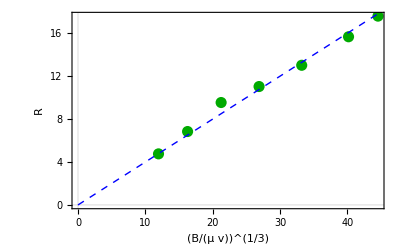

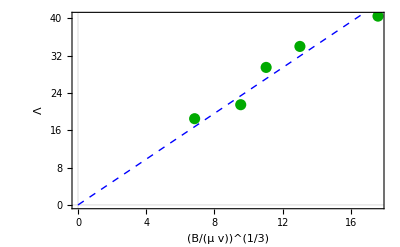

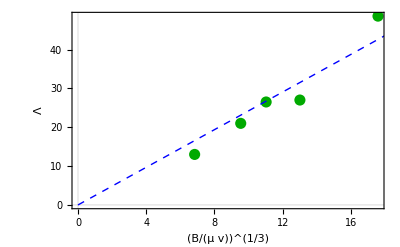

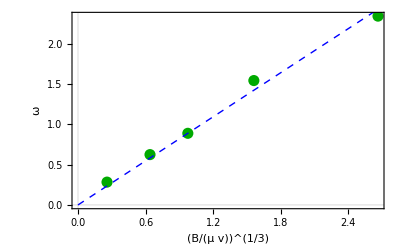

sim-data-fig2A.csv

sim-data-fig2B.csv

sim-data-fig2C.csv

sim-data-figA1A.csv

sim-data-figA1B.csv

```mathematica
Rdata = {{11.465728072610881,17.58825}, {10.34,15.666},{4.188,6.838},{3.077,4.757},{8.55,13.01},{6.92, 11.03},{5.47,9.54}};
lμdata = {{4.188, 18.5},{5.47,21.5},{6.92,29.5}, {8.55, 34},{11.465728072610881, 40.5}};
ldata = {{6.838, 18.5},{9.54,21.5},{11.03,29.5}, {13.01, 34},{17.58825, 40.5}};
velocityVSell = {{43.3075, 18.5},{33.157,21.5},{26.198,29.5}, {21.2207, 34},{11.46573,25.11321}};
Λdata =  { {6.838,13},{9.54,21.0},{11.03, 26.5},{13.01,27},{17.58825, 48.6}};

simSlope = Fit[Rdata, { y}, y][[1]]; exptSlope = 0.4; slopeRatio = simSlope/exptSlope; 
Rdata = Rdata.DiagonalMatrix[{slopeRatio,1}];
lμdata = lμdata.DiagonalMatrix[{slopeRatio,1}];
ωdata = velocityVSell[[;;,1]]/lμdata;

LRplot = ListPlot[Rdata, PlotStyle->{Darker[Green],PointSize[0.02]}, AxesOrigin->{0,0}, AxesLabel->{"   (B/(μ v))^(1/3)","R"}, PlotTheme->"Scientific", LabelStyle->Medium];
SRplot = Plot[Fit[Rdata, { y}, y]/.y->x, {x, 0.0 Min[Rdata[[;;, 1]]],Max[Rdata[[;;, 1]]]}, PlotStyle->{Blue, Thick, Dashed}];


Λplot = ListPlot[Λdata, PlotStyle->{Darker[Green],PointSize[0.02]}, AxesOrigin->{0,0}, AxesLabel->{"   (B/(μ v))^(1/3)","Λ"}, PlotTheme->"Scientific", LabelStyle->Medium];
FΛplot = Plot[Fit[Λdata, { y}, y]/.y->x, {x, 0.0 Min[Rdata[[;;, 1]]],Max[Rdata[[;;, 1]]]}, PlotStyle->{Blue, Thick, Dashed}];

lplot = ListPlot[ldata, PlotStyle->{Darker[Green],PointSize[0.02]}, AxesOrigin->{0,0}, AxesLabel->{"   (B/(μ v))^(1/3)","Λ"}, PlotTheme->"Scientific", LabelStyle->Medium];
Flplot = Plot[Fit[ldata, { y}, y]/.y->x, {x, 0.0 Min[Rdata[[;;, 1]]],Max[Rdata[[;;, 1]]]}, PlotStyle->{Blue, Thick, Dashed}];


ωplot = ListPlot[ωdata, PlotStyle->{Darker[Green],PointSize[0.02]}, AxesOrigin->{0,0}, AxesLabel->{"(B/(μ v))^(1/3)","ω"}, PlotTheme->"Scientific", LabelStyle->Medium];
ωfplot = Plot[Fit[ωdata, { y}, y]/.y->x, {x, 0.0 Min[Rdata[[;;, 1]]],Max[Rdata[[;;, 1]]]}, PlotStyle->{Blue, Thick, Dashed}];

Fit[ldata, { y}, y][[1]]
Fit[Λdata, { y}, y][[1]]

Fit[lμdata, { y}, y][[1]]
Fit[Rdata, { y}, y][[1]]
Fit[ωdata, { y}, y][[1]]

Show[LRplot, SRplot]
Show[lplot, Flplot]
Show[Λplot, FΛplot]
Show[ωplot, ωfplot]

directory = FileNameJoin[{ParentDirectory[NotebookDirectory[],2], "Run Results"}];
SetDirectory[directory];
Export["sim-data-fig2A.csv",lμdata]
Export["sim-data-fig2B.csv",Rdata]
Export["sim-data-fig2C.csv",ωdata]
Export["sim-data-figA1A.csv",ldata]
Export["sim-data-figA1B.csv",Λdata]
```

```mathematica
ωdata
```

{{2.66278,2.34095},{1.56087,1.54219},{0.974857,0.888068},{0.639105,0.624138},{0.257501,0.283104}}

```mathematica
(*Rod Relaxation*)
```

```mathematica
SetDirectory[NotebookDirectory[]];

replace[string_]:= StringReplace[string,{"e+":>"*^","e-":>"*^-"}];

replaceRaw[rawPos_]:= (replace /@ rawPos)//Flatten

(* flowRate =10. 10^-6/60;r = 0.5  10^-3;*)
rawPositions = Import["positions-relaxation-ToHelix3"  <>".dat"] ;

rawPositions1= ToExpression@StringSplit[StringJoin /@ (replaceRaw /@ rawPositions),","];

numTimeSteps =Length[rawPositions1]

Clear[positions]
positions[timeIndex_]:= ArrayReshape[rawPositions1[[timeIndex]],{(rawPositions1[[timeIndex]]//Length)/3, 3}](*.RotationMatrix[Pi/2, {0,-1,0}] *)
edgeVecs[tIndex_]:=( positions[tIndex][[2;;]] - positions[tIndex][[;;-2]])
edgeLengths[tIndex_]:=Norm /@ edgeVecs[tIndex]
edgeDirections[tIndex_]:=edgeVecs[tIndex]/edgeLengths[tIndex]

(*Calculate maximum strain on the edge*)
max[index_]:= Abs[(edgeLengths[1] - edgeLengths[index])/edgeLengths[1]]//Max  
((max /@ Range[numTimeSteps])//Max)

plot[tIndex_]:= ListPointPlot3D[{positions[1][[3;;]],Chop[positions[numTimeSteps][[3;;]]],Chop[positions[tIndex][[3;;]]]}, BoxRatios->Automatic,PlotStyle->{Thickness[0.007]}, PlotRange->{{-3.5,1},{-2,4},{-2,2}}]/.Point -> Line

Manipulate[plot[tIndex],{tIndex,1, numTimeSteps,1}]
```

96

0.000200088

```mathematica
vorLength[tIndex_][vIndex_]:=(edgeLengths[tIndex][[vIndex - 1]]+ edgeLengths[tIndex][[vIndex]])/2
curvatureBinormal[tIndex_][vIndex_]:=(2Cross[edgeDirections[tIndex][[vIndex - 1]],edgeDirections[tIndex][[vIndex]]])/(1 + edgeDirections[tIndex][[vIndex - 1]].edgeDirections[tIndex][[vIndex]])1/(vorLength[tIndex][vIndex])


curvatureBinormals[tIndex_]:= curvatureBinormal[tIndex] /@ Range[2, Length[positions[1]] - 1]
Norm /@(curvatureBinormals[numTimeSteps])
```

{0.707162,0.707259,0.707317,0.70734,0.707356,0.707487,0.707453,0.707574,0.707499,0.707756,0.707486,0.707668,0.707956,0.707511,0.707617,0.708163,0.7071,0.708609,0.708089,0.706942,0.708081,0.708058,0.706925,0.708106,0.70806,0.708576,0.706536,0.707603,0.708907,0.707995,0.707149,0.707328,0.708315,0.706365,0.709216,0.707091,0.708077,0.706489,0.706977,0.710321,0.704716,0.709883,0.705288,0.710017,0.70432,0.708904,0.706967,0.709081,0.70483,0.707853,0.708949,0.705319,0.707292,0.708577,0.707163,0.706543,0.706778,0.708397,0.705613,0.707367,0.7077,0.708276,0.705559,0.707897,0.70741,0.705442,0.707222,0.709386,0.704296,0.710518,0.703912,0.708287,0.707467,0.708191,0.706672,0.705326,0.710005,0.705432,0.706778,0.707859,0.706423,0.709094,0.704619,0.707367,0.709304,0.706502,0.706869,0.705934,0.708691,0.708175,0.704359,0.709497,0.706582,0.70731,0.707406,0.707077,0.707309,0.706546}

```mathematica
1/Sqrt[2.]
```

0.707107

```mathematica
r =1; τ = 1;
FrenetSerretSystem[{r Cos[t],r Sin[t], τ t},t]//FullSimplify
```

{{1/2,1/2},{{-Sin[t]/(√2),Cos[t]/(√2),1/(√2)},{-Cos[t],-Sin[t],0},{Sin[t]/(√2),-Cos[t]/(√2),1/(√2)}}}

```mathematica
r =1; τ = 1;numVerts = 100;
theta = Table[2 (Pi n)/(numVerts - 1.0), {n, 1, numVerts}]; 
verts = {r Cos[theta],r  Sin[theta], τ theta}//Transpose;
edgeVecs[tIndex_]:=(verts[[2;;]] - verts[[;;-2]])
edgeLengths[tIndex_]:=Norm /@ edgeVecs[tIndex]
edgeDirections[tIndex_]:=edgeVecs[tIndex]/edgeLengths[tIndex]

vorLength[tIndex_][vIndex_]:=(edgeLengths[tIndex][[vIndex - 1]]+ edgeLengths[tIndex][[vIndex]])/2
curvatureBinormal[tIndex_][vIndex_]:=(2Cross[edgeDirections[tIndex][[vIndex - 1]],edgeDirections[tIndex][[vIndex]]])/(1 + edgeDirections[tIndex][[vIndex - 1]].edgeDirections[tIndex][[vIndex]])Sqrt[2]/(vorLength[tIndex][vIndex])


curvatureBinormals[tIndex_]:= curvatureBinormal[tIndex] /@ Range[2, Length[positions[1]] - 1]
Norm /@(curvatureBinormals[numTimeSteps])
```

{0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166,0.707166}

```mathematica
(*with slightly different nearly circular random initializations. The curvature is equal for both cases*)
p1 = -Graphics3D-;p2 = -Graphics3D-;
Show[p1, p2]
```

-Graphics3D-

```mathematica
(*Sedimenting Rods*)
```

```mathematica
ClearAll["Global`*"]

SetOptions[Plot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,Thickness[0.005]}, PlotRange->All];
SetOptions[ListPlot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,PointSize[0.005]}, PlotRange->All];

SetOptions[ListPointPlot3D,LabelStyle->Directive[Black, Bold, FontSize-> 16], PlotStyle-> {Lighter[Blue],PointSize[0.005],Thickness[0.007]}, PlotRange->All];


SetOptions[ListLogPlot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,PointSize[0.005]}, PlotRange->All];
SetOptions[ListLinePlot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,Thickness[0.005]}, PlotRange->All];
SetOptions[ParametricPlot,LabelStyle->Directive[Black, Bold, Medium], PlotStyle-> {Blue,Thickness[0.005]}, PlotRange->All];

SetDirectory[NotebookDirectory[]];

replace[string_]:= StringReplace[string,{"e+":>"*^","e-":>"*^-"}];

replaceRaw[rawPos_]:= (replace /@ rawPos)//Flatten

(* flowRate =10. 10^-6/60;r = 0.5  10^-3;*)
rawPositions = Import["positions-falling-rod"  <>".dat"] ;
times = Import["times-falling-rod"  <>".dat"] ;

rawPositions1= ToExpression@StringSplit[StringJoin /@ (replaceRaw /@ rawPositions),","];

numTimeSteps =Length[rawPositions1]

Clear[positions]
positions[timeIndex_]:= ArrayReshape[rawPositions1[[timeIndex]],{(rawPositions1[[timeIndex]]//Length)/3, 3}].RotationMatrix[Pi/2, {0,-1,0}] 

wallPosition = 0.5;
viewSize = 0.05

plane = Graphics3D[{ Purple,Opacity[0.1], InfinitePlane[{{0,0,-wallPosition},{1,0,-wallPosition},{0,1,-wallPosition}}]}, AspectRatio->1(*, Axes->True*)];

plot[tIndex_]:= ListPointPlot3D[{positions[1][[3;;]],Chop[positions[numTimeSteps][[3;;]]],Chop[positions[tIndex][[3;;]]]}, BoxRatios->Automatic,PlotStyle->{Thickness[0.007]}, PlotRange->{{-viewSize,viewSize},{-viewSize,viewSize},{0.01,-1.1 wallPosition}}]/.Point -> Line

Manipulate[Show[plot[tIndex], plane],{tIndex,1, numTimeSteps,1}]
```

100

0.05

```mathematica
(*Simulation for buckling of filament due to fluid*)
```

```mathematica
SetDirectory[NotebookDirectory[]];

replace[string_]:= StringReplace[string,{"e+":>"*^","e-":>"*^-"}];

replaceRaw[rawPos_]:= (replace /@ rawPos)//Flatten

(* flowRate =10. 10^-6/60;r = 0.5  10^-3;*)
rawPositions = Import["positions-fluidBuckling"  <>".dat"] ;

rawPositions1= ToExpression@StringSplit[StringJoin /@ (replaceRaw /@ rawPositions),","];

numTimeSteps =Length[rawPositions1];

Clear[positions]
positions[timeIndex_]:= ArrayReshape[rawPositions1[[timeIndex]],{(rawPositions1[[timeIndex]]//Length)/3, 3}].RotationMatrix[Pi/2, {0,-1,0}] 

initLength =Total[ Norm /@ (positions[1][[2;;]] - positions[1][[;;-2]])];


viewSize = 0.5 initLength;


plot[tIndex_]:= ListPointPlot3D[{Chop[positions[tIndex][[3;;]]], Chop[positions[numTimeSteps][[3;;]]]}, BoxRatios->Automatic,PlotStyle->{{Thickness[0.007],Blue}, {Thickness[0.007],Green}}, PlotRange->{{-viewSize,viewSize},{-viewSize,viewSize},{0.25 initLength,- initLength}}]/.Point -> Line

Manipulate[Show[plot[tIndex]],{tIndex,1, numTimeSteps,1}]
```

Show::gtype: plot is not a type of graphics.

```mathematica
Y = 2700; r = 0.5 10^-3; μ = 0.001; 
 B = Pi/4 Y r^4; v = 0.02;
lc = 1.41(B/(μ v) )^(1/3)
l = 0.024;
ratio = l(B/(μ v) )^(-1/3)
l = 0.0245;
ratio = l(B/(μ v) )^(-1/3)
```

0.0264842

1.27774

1.30436

```mathematica
(1.2777425358896257 + 1.3043621720539929)/2
```

1.29105

```mathematica
lengths[timeIdx_] := Norm /@ (positions[timeIdx][[2;;]] - positions[timeIdx][[;;-2]]);
strain[timeIdx_] :=Abs[(lengths[timeIdx] - lengths[1])/lengths[1]]
strain /@ Range[numTimeSteps]//Max
```

0.0000800106

```mathematica
β = 3.48;
FindRoot[(β B)/(2 Pi μ v)==L^3/Log[L/r] ,{ L,0.02}]
```

{L→0.0242413}